# Impedance

## Černá skříňka - přenos, impedance

```mathematica
(* Příklad 8 *)
(* Napětí na vstupu černé skříňky je 10+5,6j V,napětí na výstupu je 0,1+0,03j V. Určete přenos černé skříňky. *)
-Graphics-;
ClearAll["Global`*"]
Uin = 10+5.6*ⅉ
Uout = 0.1+0.03ⅉ

Prenos  = Abs[Uout/Uin]
Prenos  = Uout/Uin
```

10.+5.6 ⅈ

0.1+0.03 ⅈ

0.00910923

0.0088916-0.00197929 ⅈ

```mathematica
(* Příklad 9 *)
(* Napětí na svorkách černé skříňky je 10+5,6j V,skříňkou teče proud 0,1+0,03j A.Určete impedanci černé skříňky. *)
-Graphics-;
ClearAll["Global`*"]
Uin = 10+5.6*ⅉ
Ics = 0.1+0.03ⅉ

Zcs = Uin/Ics
```

10.+5.6 ⅈ

0.1+0.03 ⅈ

107.156+23.8532 ⅈ

## Impedance - příklady na výpočet impedance

```mathematica
(* Příklad 10 *)
-Graphics-
(*
Hodnoty součástek:C1=C2=100 nF,R1=0.1 Ω,L1=50 μH.
1. Spočítejte a vyneste do grafu vstupní impedanci obvodu pro 10^4 ω≤10^8.
*)
```

1/10000000

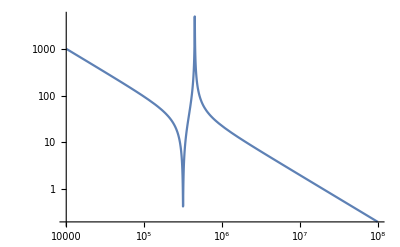

```mathematica
ClearAll["Global`*"]
C1=100*10^-9;
C2=100 *10^-9
R1 = 0.1;
L1 = 50*10^-6;

ZR1 = R1;
ZL1 = ⅉ*ω*L1;
ZC1 = 1/(ⅉ*ω*C1);
ZC2 = 1/(ⅉ*ω*C2);

ZR1L1 = ZR1+ZL1;
ZR1L1C2 = (ZR1L1*ZC2)/(ZR1L1+ZC2);


Zin = ZC1+ZR1L1C2;

LogLogPlot[Abs[Zin],{ω,10^4,10^8}]
```

```mathematica
(* Příklad 11 *)
```

```mathematica
-Graphics-
(*
Hodnoty součástek:R1=R3=0.1 Ω,R2=1000 Ω,L1=L2=1 mH,C1=1 μF.
1. Vykreslete přenos obvodu pro 1≤ω≤10^8.
*)
```

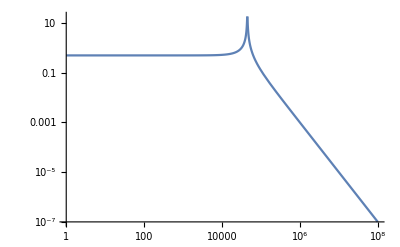

```mathematica
ClearAll["Global`*"]
R1=R3=0.1;
R2=1000;
L1=L2=1*10^-3;
C1=1*10^-6;

ZR1 = R1;
ZR2 = R2;
ZR3 = R3;
ZL1 = ⅉ*ω*L1;
ZL2 = ⅉ*ω*L2;
ZC1 = 1/(ⅉ*ω*C1);

ZR3L2 = ZR3+ZL2;

Zout = 1/(1/ZR2+1/ZR3L2+1/ZC1);
Zin = ZR1+ZL1+Zout;

Prenos = Zout/Zin;
LogLogPlot[Abs[Prenos],{ω,1,10^8}]
```

```mathematica
(* Příklad 13 *)
-Graphics-
(*
Hodnoty součástek:R1=R2=0.1 Ω,C1=C2=100 μF,L1=50 μH,L2=500 nH.
1.Vykreslete přenos obvodu pro 1≤ω≤10^8.
2. Spočítejte a vyneste do grafu vstupní impedanci obvodu pro 1≤ω≤10^8.
*)
```

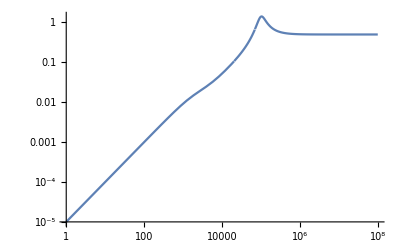

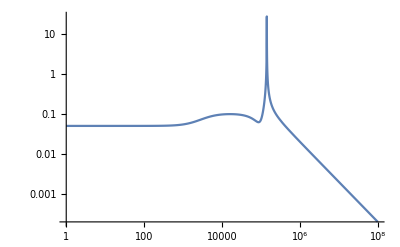

```mathematica
ClearAll["Global`*"]
R1=R2=0.1;
C1=C2=100*10^-6;
L1 = 50*10^-6;
L2 = 500*10^-9;

ZR1 = R1;
ZR2 = R2;
ZC1 = 1/(ⅉ*ω*C1);
ZC2 = 1/(ⅉ*ω*C2);
ZL1 = ⅉ*ω*L1;
ZL2 = ⅉ*ω*L2;

Zout = 1/(1/ZL2+1/ZC2);
ZR1L1 = ZR1+ZL1;
ZR2R1L1C1 = 1/(1/ZR2+1/ZR1L1+1/ZC1);
Zin = ZR2R1L1C1+Zout;

Prenos = Zout/Zin;

LogLogPlot[Abs[Prenos],{ω,1,10^8}]
LogLogPlot[Abs[Zin],{ω,1,10^8}]
```

## Impedance - náhradní zapojení

```mathematica
(* Příklad 14 *)
(*
Impedance mezi dvěma svorkami je Z=2000+300*ⅉ Ω.
1. Určete parametry sériového náhradního schématu pro ω=100 s^-1
2. Jaké to budou součástky a jaké budou mít parametry?
*)

ClearAll["Global`*"]
(* obecné vysvětlení *)
Rx = 100;
ZRx = Rx ; (* reálná část impedance je hodnota odporu rezistoru *)
ZLx = +ⅉ*ω*Lx;
ZCx = 1/(ⅉ*ω*Cx)-> ⅉ/ⅉ*1/(ⅉ*ω*Cx)-> ⅉ/(ⅉ^2*ω*Cx)-> ⅉ/(-1*ω*Cx)-> -ⅉ*1/(ω*Cx)
```

```mathematica
ClearAll["Global`*"]
Z=2000+ⅉ*300;
R1=Re[Z];
L1 = Im[Z]/ω/. ω->100;
Print["Náhradní sériové zapojení je tvořeno rezistorem R1 a cívkou L1, hodnoty součástek jsou R1 = ",R1, " Ω a L1 = ",L1, " H."]
```

Náhradní sériové zapojení je tvořeno rezistorem R1 a cívkou L1, hodnoty součástek jsou R1=2000 Ω a L1=3 H.

```mathematica
(* Příklad 15 *)
(*
Impedance mezi dvěma svorkami je Z=800-ⅉ*500 Ω.
1. Určete parametry sériového náhradního schématu pro ω=10000 s^-1
2. Jaké to budou součástky a jaké budou mít parametry?
*)
```

```mathematica
ClearAll["Global`*"]
Z=800-ⅉ*500;
R1 =Re[Z];
C1 = -1/(ω*Im[Z])/.ω->10^4//N;
Print["Náhradní sériové zapojení je tvořeno rezistorem R1 a kondenzátorem C1, hodnoty součástek jsou R1 = ",R1, " Ω a C1= ",C1, " F."]
```

Náhradní sériové zapojení je tvořeno rezistorem R1 a kondenzátorem C1, hodnoty součástek jsou R1 = 800 Ω a C1= 2.×10^-7 F.